# Wigner Function Reconstruction

## Last Updated: 2025/04/23

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

```mathematica
(*todo: implement padding, interpolating/resampling, rescale wigner axes/chop*)
```

```mathematica
(*todo: may need ot rescale before zero-padding*)
```

```mathematica
(*todo: resampling doesn't seem to be extend FFT axes correctly*)
```

# General

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

## Functions

## General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

## Phonon Conversion

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
(*CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];*)
CoherentCFunc=Interpolation[Transpose[{coherentX0,coherentY0}]];
CoherentC[x_]:=CoherentCFunc[#]&[Clip[x,{0.,0.8}]];
```

## Dataset Processing

### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Join@@{
Import[filenameDJ,{"Attributes","/arguments"}],
Import[filenameDJ,{"Attributes","/parameters"}]
};

Return[{datasetRaw,parameterList}];
];
```

### Processing

```mathematica
(*threshold counts into s-state vs d-state probability*)
Options[ThresholdCounts]={
"Threshold"->-1
};
ThresholdCounts[dataset_List,countsColumn_Integer,OptionsPattern[]]:=Module[
{
results=dataset,

(*find state discrimination threshold*)
countThreshold=If[
OptionValue["Threshold"]!=-1,
OptionValue["Threshold"],
FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"]
]
},

(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
CollateData[dataset_List,groupColumnList_List]:=GroupBy[dataset,
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],
N[Mean[#]]&
]//KeySort;
```

### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

## Batch Processing

```mathematica
(*(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS[filedir_,filekey_]:=Module[
{
(*actual data*)
(*datafile=ImportDatasetARTIQ[filedir,ToString[filekey]],*)
datafile,
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*import dataset*)
datafile=ImportDatasetARTIQ[filedir,ToString[filekey]];

(*extract heating time from parameter list*)
heatingTimeSeconds=datafile[[2]]["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[datafile[[1]]]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->datafile[[2]],
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datafile,datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
(*Remove[datafile];*)
ClearSystemCache[];

(*return dataset*)
Return[results];
];*)
```

```mathematica
(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS2[dataset_List,parameterList_Association]:=Module[
{
(*actual data*)
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*extract heating time from parameter list*)
heatingTimeSeconds=parameterList["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[dataset]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->parameterList,
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
ClearSystemCache[];

(*return dataset*)
Return[results];
];
```

# Functions etc.

## FFT-Related

```mathematica
(*recenter a 2D matrix after fourier transform*)
RecenterFourier[data_List]:=RotateRight[
data,
{#1,#2}
][[;;#1*2,;;#2*2]]&@@Floor[Dimensions[data]/2];
```

```mathematica
(*chop off a 2D matrix a lá w/RecenterFourier, but without rotation*)
CutoffGrid[data_List]:=data[[;;#1*2,;;#2*2]]&@@Floor[Dimensions[data]/2];
```

## Plotting

```mathematica
(*create color scaling for χ(β) plot*)
colorFuncName="DefaultColorFunction"/.(Method/.Charting`ResolvePlotTheme[Automatic,ListDensityPlot]);
colorFunc=ColorData[colorFuncName]@Rescale[#,{-1.,1.},{0.,1.0}]&;
(*create corresponding bar legend*)
colorLegend=BarLegend[{colorFunc,{-1.,1.}}];
```

```mathematica
(*alternate color scaling for χ(β) plot*)
colorFuncName="TemperatureMap";
colorFunc=ColorData[colorFuncName]@Rescale[#-0.,{-1.,1.}/1.,{0.,1.0}]&;
(*create corresponding bar legend*)
colorLegend=BarLegend[{colorFunc,{-1.,1.}}];
```

## ListDensityPlot (2D) - Convenience

```mathematica
(*ListDensityPlot convenience function*)
Remove[Plot2DResults];

(*specify optional arguments and their default value for Plot2D function*)
Options[Plot2DResults]={
(*{{title_label},{x_label},{y_label}}*)
"AxesLabels"->{{""},{""},{""}},
"ImageSize"->Scaled[0.35]
(*"ImageScale"->0.35*)
(*"args"->None*)
};

(*Plot2DResults[data_List,args___:None,OptionsPattern[]]:=Block[*)
Plot2DResults[data_List,OptionsPattern[{Options[Plot2DResults],ListDensityPlot}]]:=Block[
{
(*expand some keyword arguments for convenience*)
AxesLabelVals=OptionValue["AxesLabels"]
},

(*create listdensityplot*)
ListDensityPlot[
data,
PlotLegends->Placed[colorLegend,Bottom],
PlotRange->{
{Full,Full},
{Full,Full},
{-1.0,1.0}
},
ColorFunction->colorFunc,
ColorFunctionScaling->False,
InterpolationOrder->0,
Mesh->None,
FrameLabel->{ 
{Style[AxesLabelVals[[1,1]],{Black,Directive[18]}],None},
{
Style[AxesLabelVals[[2,1]],{Black,Directive[18]}],
Style[AxesLabelVals[[3,1]],{Black,Directive[15]}]
}
},
AspectRatio->0.9,
(*ImageSize->{450,450}*)
(*ImageSize->Scaled[0.25]*)
ImageSize->OptionValue["ImageSize"]
(*
(*pass all function arguments down to ListDensityPlot*)
args*)
]
];
```

## ListPlot3D (3D) - Convenience

```mathematica
(*ListPlot3D convenience function*)
Remove[Plot3DResults];

(*specify optional arguments and their default value for Plot2D function*)
Options[Plot3DResults]={
(*{{title_label},{x_label},{y_label}}*)
"AxesLabels"->{{""},{""},{""}},
"ImageSize"->Scaled[0.35]
(*"args"->None*)
};

(*Plot2DResults[data_List,args___:None,OptionsPattern[]]:=Block[*)
Plot3DResults[data_List,OptionsPattern[{Options[Plot3DResults],ListDensityPlot}]]:=Block[
{
(*expand some keyword arguments for convenience*)
AxesLabelVals=OptionValue["AxesLabels"]
},

(*create listdensityplot*)
ListPlot3D[
data,
PlotLegends->Placed[colorLegend,Bottom],
PlotRange->{
{Full,Full},
{Full,Full},
{-1.0,1.0}
},
ColorFunction->colorFunc,
ColorFunctionScaling->False,
InterpolationOrder->2,
Mesh->None,
(*FrameLabel->{ 
{Style[AxesLabelVals[[1,1]],{Black,Directive[18]}],None},
{
Style[AxesLabelVals[[2,1]],{Black,Directive[18]}],
Style[AxesLabelVals[[3,1]],{Black,Directive[15]}]
}
},*)
AspectRatio->0.9,
(*ImageSize->{450,450}*)
ImageSize->OptionValue["ImageSize"]
(*
(*pass all function arguments down to ListDensityPlot*)
args*)
]
];
```

# User Input

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2025-04\\2025-04-24";
(*directoryString="/Volumes/groups/motion/Data/2025-04/2025-04-22";*)
```

```mathematica
(*list of RIDs to analyze*)
ridList={107229};
```

```mathematica
(*convert time to displacement*)
α0={50.,√2.520};
(*α0={60.,√2.723};*)
```

```mathematica
(*dataset columns*)
countCol=2;
heraldCol=3;
timeCol=5;
phaseCol=6;
axisCol=7;
```

```mathematica
countCol=2;
heraldCol=2;
timeCol=3;
phaseCol=4;
axisCol=1;
```

# Import & Preprocess

## Batch Import

```mathematica
(*batch import*)
AbsoluteTiming[
datafileList=ImportDatasetARTIQ[
directoryString,
ToString[#]
]&/@ridList;
]
```

{0.231048,Null}

```mathematica
(*combine all datasets for value check*)
dataset=Join@@datafileList[[;;,1]];
```

```mathematica
(*(*warning: this bit deprecated - only for data before 2025/04*)
(*separate datasets by real vs imag and combine*)
datasetsSorted=GroupBy[datafileList,(#[[2]]["enable_pulse3_sigmax"]&)->First];
datasetReal=Join@@datasetsSorted[0];
datasetImag=Join@@datasetsSorted[1];*)
```

```mathematica
(*separate datasets by real vs imag*)
datasetsSorted=GroupBy[dataset,#[[axisCol]]&];
datasetReal=datasetsSorted[0.];
datasetImag=datasetsSorted[1.];
```

```mathematica
(*set parameters as simply the first dataset's*)
parameters=(First@datafileList)[[2]];
```

## Verify Data

```mathematica
(*ListLinePlot[dataset[[#1;;#2,2]],PlotRange->Full]&[
IntegerPart[0.02*Length[dataset]],
IntegerPart[0.051*Length[dataset]]
]*)
```

```mathematica
(*(*remove bad data*)
th0=dataset;
tha1=dataset[[;;IntegerPart[0.020*Length[dataset]]]];
tha2=dataset[[IntegerPart[0.051*Length[dataset]];;]];
dataset=Join[tha1,tha2];*)
```

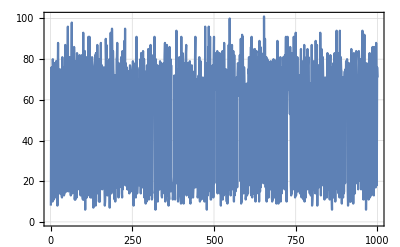
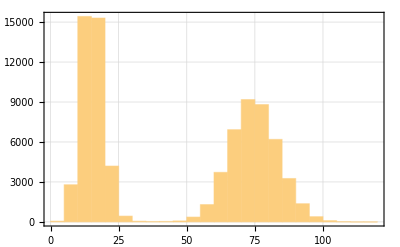
{(0. | 8. | 6709. | 14325.
0. | 71. | 20804. | 10068.
0. | 67. | 4160. | 62180.),-Graphics-,-Graphics-}

```mathematica
(*value check*)
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;;;Min[Round[Length[#]/1000],1000]]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,countCol]]]
```

```mathematica
(*extract important parameters*)
attCatDB=First@parameters["atts_cat_db"];
amplCatPCT=First@parameters["ampls_cat_pct"];
```

# χ(β) (Characteristic Function) Display

## Prepare Functions

## Process

```mathematica
(*round the grid values after converting from radial to rectangular co-ordinates*)
βStepRound=0.07;
```

```mathematica
(*todo: maybe group by r,θ first, then convert to x?*)
```

## Preprocess

```mathematica
(*select heralded if we enable herald*)
{datasetProcessedReal,datasetProcessedImag}={datasetReal,datasetImag};
```

```mathematica
(*threshold dataset counts into P_↓*)
{datasetProcessedReal,datasetProcessedImag}=ThresholdCounts[
#[[;;,{timeCol,phaseCol,countCol}]],
3
]&/@{datasetProcessedReal,datasetImag};
```

```mathematica
(*(*convert parameter units*)
{datasetProcessedReal,datasetProcessedImag}=Transpose[
Transpose[#]*{(1.*^-3),1./(2^16-1.),1.}(*t_ns->t_μs, pow->turns, counts*)
]&/@{datasetProcessedReal,datasetProcessedImag};*)
```

```mathematica
(*convert P_↓ to ⟨χ(β)⟩*)
datasetProcessedReal[[;;,3]]=2.*datasetProcessedReal[[;;,3]]-1.;
datasetProcessedImag[[;;,3]]=2.*datasetProcessedImag[[;;,3]]-1.;
```

## extra inset

```mathematica
(*collate data BEFORE processing {r,θ}=>{x,y}*)
datasetProcessedReal2=datasetProcessedReal;
datasetProcessedReal2=CollateData[
datasetProcessedReal,
{1,2}
];
(*flatten back into a list*)
datasetProcessedReal2=Values@Values@datasetProcessedReal2;
datasetProcessedReal2=Flatten[datasetProcessedReal2,1];
```

```mathematica
(*convert parameter units*)
datasetProcessedReal2=Transpose[
Transpose[datasetProcessedReal2]*
{(1.*^-3),1./(2^16-1.),1.}(*t_ns->t_μs, pow->turns, counts*)
];
```

```mathematica
(*convert {r,θ} to {x,y}*)
kka=datasetProcessedReal2[[;;,1]]*Exp[ⅈ*(2.π)*(datasetProcessedReal2[[;;,2]]-0.)]*α0[[2]]/α0[[1]];
{kkx,kky}={Re[kka],Im[kka]};
{kgradx,kgrady}=(Max[#]-Min[#])/Length[#]&/@{kkx,kky};
```

```mathematica
datasetProcessedReal2[[;;,;;2]]=Round[

βStepRound
];
%//Dimensions
```

## Convert Radial Co-ordinates to Rectangular

```mathematica
(*convert {r,θ} coordinates to {x,y} and round time values to nearest βStepRound*)
datasetProcessedReal[[;;,;;2]]=Round[
{Re[#],Im[#]}&/@(datasetProcessedReal[[;;,1]]*Exp[ⅈ*(2.π)*(datasetProcessedReal[[;;,2]]-0.)])*(α0[[2]]/α0[[1]]),
βStepRound
];
datasetProcessedImag[[;;,;;2]]=Round[
{Re[#],Im[#]}&/@(datasetProcessedImag[[;;,1]]*Exp[ⅈ*(2.π)*(datasetProcessedImag[[;;,2]]-0.)])*(α0[[2]]/α0[[1]]),
βStepRound
];
```

## Prepare for Display

```mathematica
(*group datasets by x, then y*)
{datasetProcessedReal,datasetProcessedImag}=CollateData[
#,
{1,2}
]&/@{datasetProcessedReal,datasetProcessedImag};
```

```mathematica
(*sort data correctly*)
{datasetProcessedReal,datasetProcessedImag}=KeySort[#]&/@{datasetProcessedReal,datasetProcessedImag};
{datasetProcessedReal,datasetProcessedImag}=(KeySort/@#)&/@{datasetProcessedReal,datasetProcessedImag};
{datasetProcessedReal,datasetProcessedImag}=(Values@Values@#)&/@{datasetProcessedReal,datasetProcessedImag};
```

```mathematica
(*(*tmp remove - reverse for hermeticity*)
{dsTMPReal,dsTMPImag}={datasetProcessedReal[[;;,;;,3]],datasetProcessedImag[[;;,;;,3]]};
{dsTMPReal,dsTMPImag}=Reverse[#,{1,2}]&/@{dsTMPReal,dsTMPImag};
tmpLengthDJ=IntegerPart[Length[dsTMPReal]/2];

(*reverse real - note: have to do it this way b/c otherwise problem*)
dsTMPReal[[;;,-tmpLengthDJ;;]]=0.;
datasetProcessedReal[[;;,;;tmpLengthDJ,3]]=0.;
datasetProcessedReal[[;;, ;;,3]]+=dsTMPReal;

(*reverse imag - note: have to do it this way b/c otherwise problem*)
dsTMPImag[[;;,-tmpLengthDJ;;]]=0.;
datasetProcessedImag[[;;, ;;tmpLengthDJ,3]]=0.;
(*datasetProcessedImag[[;;,;;,3]]-=dsTMPImag;*)
datasetProcessedImag[[;;,;;,3]]=datasetProcessedReal[[;;,;;,3]];
(*tmp remove - reverse for hermeticity*)*)
```

```mathematica
(*store grid-ed dataset before flattening for display*)
{dsCharRe,dsCharIm}={datasetProcessedReal,datasetProcessedImag};
{datasetProcessedReal,datasetProcessedImag}=Flatten[#,1]&/@{datasetProcessedReal,datasetProcessedImag};
```

```mathematica
(*ensure values are rounded correctly, again to βStepRound (esp. after collation, b/c it averages them)*)
datasetProcessedReal[[;;,;;2]]=Round[datasetProcessedReal[[;;,;;2]],βStepRound];
datasetProcessedImag[[;;,;;2]]=Round[datasetProcessedImag[[;;,;;2]],βStepRound];
```

## Summary Statistics

```mathematica
{charReMax,charImMax}=Max/@{datasetProcessedReal[[;;,3]],datasetProcessedImag[[;;,3]]}
{charReMin,charImMin}=Min/@{datasetProcessedReal[[;;,3]],datasetProcessedImag[[;;,3]]}
{charReAvg,charImAvg}=Mean/@{datasetProcessedReal[[;;,3]],datasetProcessedImag[[;;,3]]}
{charReStd,charImStd}=StandardDeviation/@{datasetProcessedReal[[;;,3]],datasetProcessedImag[[;;,3]]}
```

{0.8,0.8}

{-0.9,-0.9}

{-0.0452,-0.0452}

{0.383223,0.383223}

## Plot

```mathematica
(*plot χ(β) separately for Re[χ(β)] and Im[χ(β)]*)
{dsChi3DPlotReal,dsChi3DPlotImag}=MapThread[
Plot2DResults[
#1,
AxesLabels->{{"Im[β]"},{"Re[β]"},{"Characteristic Reconstruction - "<>#2<>"\nRID(s): "<>ToString[ridList]}},
ImageSize->Scaled[0.35]
]&,
{
{datasetProcessedReal,datasetProcessedImag},
{"Re[χ(β)]","Im[χ(β)]"}
}
];
```

## Show

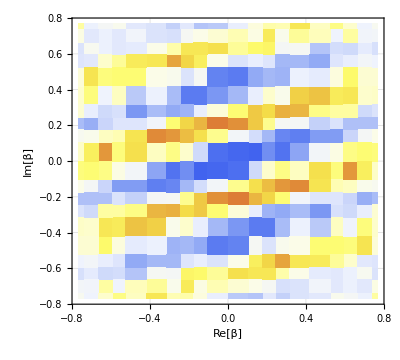
{-Graphics-,-Graphics-}

```mathematica
{dsChi3DPlotReal,dsChi3DPlotImag}
```

# Wigner Function Reconstruction

```mathematica
(*todo: make sure resampling DOES ACTUALLY SAMPLE ONTO A FUCKING SQUARE*)
(*todo: come up with a better way of specifying the x- and y- positions instead of fucking fitting*)
(*todo: allow user to set arbitrary full image ranges (e.g. to match images onto same grid for video) instead of resampling*)
```

```mathematica
(*number of zero-values to pad matrix in EACH direction*)
numZeroPad=50;
```

```mathematica
(*total grid length to extend via resampling*)
numResampleExtend=0;
```

## Preprocess for FFT

## Resample/Interpolate Onto Identical Square Grid

### Real Part

```mathematica
(*real value dimensions*)
xDimResample=Max[Length[dsCharRe[[;;,1,1]]],numResampleExtend];
yDimResample=Max[Length[dsCharRe[[1,;;,2]]],numResampleExtend];
```

```mathematica
(*interpolate results - real*)
dsCharRe2=Transpose[
Table[
ArrayResample[
dsCharRe[[;;,;;,i]],
{xDimResample,yDimResample}
],
{i,3}
],
{3,1,2}
(*{3,2,1}*)
];
```

### Imaginary Part

```mathematica
(*imag value dimensions*)
xDimResample=Max[Length[dsCharIm[[;;,1,1]]],numResampleExtend];
yDimResample=Max[Length[dsCharIm[[1,;;,2]]],numResampleExtend];
```

```mathematica
(*interpolate results - imag*)
dsCharIm2=Transpose[
Table[
ArrayResample[
dsCharIm[[;;,;;,i]],
{xDimResample,yDimResample}
],
{i,3}
],
{3,1,2}
(*{3,2,1}*)
];
```

```mathematica
(*(*tmp remove-rotate*)
dsCharIm2[[;;,;;,3]]=Reverse[dsCharIm2[[;;,;;,3]],1];
(*tmp remove-rotate*)*)
```

## Zero-Pad & Rescale Axes

### Real Part

```mathematica
(*zero pad grid results*)
dsCharReWigner=Transpose[
(*ArrayPad[#,numZeroPad]&/@Transpose[dsCharRe,3<->1],*)
ArrayPad[#,numZeroPad]&/@Transpose[dsCharRe2,3<->1],
3<->1
];
(*get dimensions of the axes*)
lengthXDim=Length[dsCharReWigner[[;;,1,1]]];
lengthYDim=Length[dsCharReWigner[[1,;;,2]]];
```

```mathematica
(*extend x-axes correctly*)
gridXVals=dsCharReWigner[[numZeroPad+1;;-(numZeroPad+1),numZeroPad+1,1]];
grixXidx=Range[lengthXDim][[numZeroPad+1;;-(numZeroPad+1)]];
gridXFit=LinearModelFit[
Transpose[{grixXidx,gridXVals}],
{1,x},
x
];
```

```mathematica
AbsoluteTiming[
Do[
dsCharReWigner[[i,;;,1]]=gridXFit[#]&/@Range[lengthXDim]//Chop,
{i,lengthXDim}
];
]
```

{0.373813,Null}

```mathematica
(*extend y-axes correctly*)
gridYVals=dsCharReWigner[[numZeroPad+1,numZeroPad+1;;-(numZeroPad+1),2]];
grixYidx=Range[lengthYDim][[numZeroPad+1;;-(numZeroPad+1)]];
gridYFit=LinearModelFit[
Transpose[{grixYidx,gridYVals}],
{1,y},
y
];
```

```mathematica
AbsoluteTiming[
Do[
dsCharReWigner[[;;,i,2]]=gridYFit[#]&/@Range[lengthYDim]//Chop,
{i,lengthYDim}
];
]
```

{0.339397,Null}

```mathematica
(*calculate axes rescaling - real - x and y*)
dsCharReWigner[[;;,;;,1]]*=1.*π/(lengthXDim*(gridXFit["BestFitParameters"][[2]])^2);
dsCharReWigner[[;;,;;,2]]*=1.*π/(lengthYDim*(gridYFit["BestFitParameters"][[2]])^2);
```

### Imaginary Part

```mathematica
(*zero pad grid results*)
dsCharImWigner=Transpose[
(*ArrayPad[#,numZeroPad]&/@Transpose[dsCharIm,3<->1],*)
ArrayPad[#,numZeroPad]&/@Transpose[dsCharIm2,3<->1],
3<->1
];
(*get dimensions of the axes*)
lengthXDim=Length[dsCharImWigner[[;;,1,1]]];
lengthYDim=Length[dsCharImWigner[[1,;;,2]]];
```

```mathematica
(*extend x-axes correctly*)
gridXVals=dsCharImWigner[[numZeroPad+1;;-(numZeroPad+1),numZeroPad+1,1]];
grixXidx=Range[lengthXDim][[numZeroPad+1;;-(numZeroPad+1)]];
gridXFit=LinearModelFit[
Transpose[{grixXidx,gridXVals}],
{1,x},
x
];
```

```mathematica
AbsoluteTiming[
Do[
dsCharImWigner[[i,;;,1]]=gridXFit[#]&/@Range[lengthXDim]//Chop,
{i,lengthXDim}
];
]
```

{0.388161,Null}

```mathematica
(*extend y-axes correctly*)
gridYVals=dsCharImWigner[[numZeroPad+1,numZeroPad+1;;-(numZeroPad+1),2]];
grixYidx=Range[lengthYDim][[numZeroPad+1;;-(numZeroPad+1)]];
gridYFit=LinearModelFit[
Transpose[{grixYidx,gridYVals}],
{1,y},
y
];
```

```mathematica
AbsoluteTiming[
Do[
dsCharImWigner[[;;,i,2]]=gridYFit[#]&/@Range[lengthYDim]//Chop,
{i,lengthYDim}
];
]
```

{0.327727,Null}

```mathematica
(*calculate axes rescaling - imag - x and y*)
dsCharImWigner[[;;,;;,1]]*=1.*π/(lengthXDim*(gridXFit["BestFitParameters"][[2]])^2.);
dsCharImWigner[[;;,;;,2]]*=1.*π/(lengthYDim*(gridYFit["BestFitParameters"][[2]])^2.);
```

## 2D FFT for Wigner

```mathematica
(*combine Re[χ(β)] and Im[χ(β)] for 2D FFT! and rotate correctly!*)
AbsoluteTiming[
(*note: use a holder instead of directly modifying dsWigner b/c it costs ~100x overhead*)
wignerValsTMP=RecenterFourier[
Fourier[
1.*dsCharReWigner[[;;,;;,3]]+1.*ⅈ*dsCharImWigner[[;;,;;,3]],
FourierParameters->{1,-1}(*no normalization, but reverse transform*)
(*rescale wigner function correctly - exclude zero-padded points for energy conservation*)
]
];
]
AbsoluteTiming[
(*dsWigner[[;;,;;,3]]/=(Times@@Dimensions[dsCharRe2[[;;,;;,1]]])^0.5;*)
wignerValsTMP/=(Times@@Dimensions[dsCharRe2[[;;,;;,1]]])^0.5;
(*also rescale for max contrast lol*)
wignerValsTMP/=Max[Abs[wignerValsTMP]];
(*wignerValsTMP/=10.;*)
]
```

{0.0035337,Null}

{0.0001868,Null}

```mathematica
(*prepare XY grid for fourier (to ensure same dimensionality)*)
AbsoluteTiming[
dsWigner=CutoffGrid[dsCharReWigner];
(*insert wigner vals actual*)
dsWigner[[;;,;;,3]]=wignerValsTMP;
]
```

{0.0022353,Null}

## Plot

```mathematica
(*create listdensityplot data*)
dsWignerPlotDataReal=Flatten[dsWigner,1];
dsWignerPlotDataReal[[;;,3]]=Re[dsWignerPlotDataReal[[;;,3]]];
dsWignerPlotDataImag=Flatten[dsWigner,1];
dsWignerPlotDataImag[[;;,3]]=Im[dsWignerPlotDataImag[[;;,3]]];
dsWignerPlotDataAbs=Flatten[dsWigner,1];
dsWignerPlotDataAbs[[;;,3]]=Abs[dsWignerPlotDataAbs[[;;,3]]];
dsWignerPlotDataArg=Flatten[dsWigner,1];
dsWignerPlotDataArg[[;;,3]]=Arg[dsWignerPlotDataArg[[;;,3]]]/π;
```

```mathematica
(*plot Wigner*)
AbsoluteTiming[
{dsWignerAbs3DPlot,dsWignerArg3DPlot,dsWignerRe3DPlot,dsWignerIm3DPlot}=
MapThread[
Plot2DResults[
#1,
AxesLabels->{{"Im[γ]"},{"Re[γ]"},{"Wigner Reconstruction - "<>#2<>"\nRID(s): "<>ToString[ridList]}},
ImageSize->Scaled[0.31]
]&,
{
{dsWignerPlotDataAbs,dsWignerPlotDataArg,dsWignerPlotDataReal,dsWignerPlotDataImag},
{"Abs[W(γ)]","Arg[W(γ)]","Re[W(γ)]","Im[W(γ)]"}
}
];
]
```

{3.55532,Null}

## Show

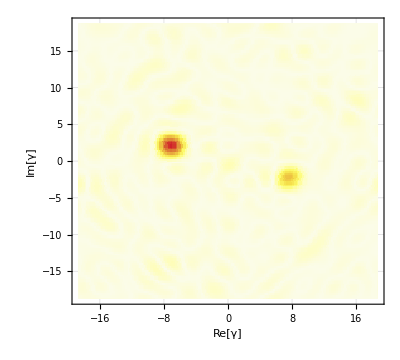
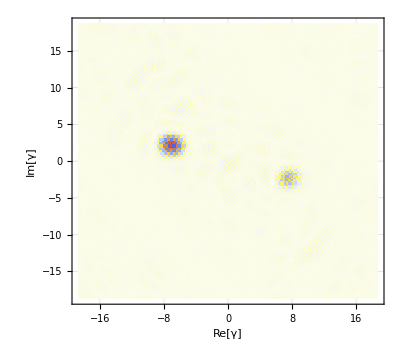
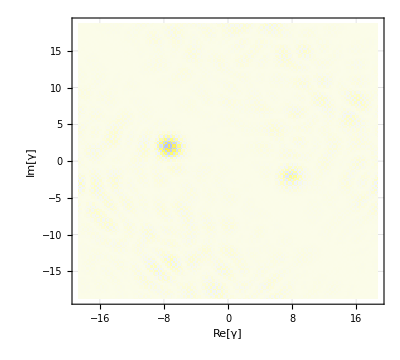

```mathematica
{dsWignerAbs3DPlot,(*dsWignerArg3DPlot,*)dsWignerRe3DPlot,dsWignerIm3DPlot}
```

# Actual Image Processing - Characteristic Must First Run

## Helpful Functions

```mathematica
(*create colored image*)
ColorImage[data_List]:=With[
{dataRGB=Map[
List@@colorFunc[#]&,
data/((*Max[data]*)1.),
{2}
]},
Return[
Image[dataRGB,ImageSize->Scaled[0.3]]
];
];
```

## Configuration

```mathematica
(*configuration*)
zeroPad=50;
resampleFactor=1;
```

```mathematica
(*filterfunctmp[img_]:=LowpassFilter[img,2.];*)
```

```mathematica
filterfunc1[img_]:=img;(*GaussianFilter[img,2.];*)
```

```mathematica
filterfunc2[img_]:=img;(*GaussianFilter[img,3.];*)
```

```mathematica
θrot=0.;
```

## Process Characteristic Image

```mathematica
(*get data points as matrix*)
{matRawRe,matRawIm}={dsCharRe[[;;,;;,3]],dsCharIm[[;;,;;,3]]};
```

```mathematica
(*upsample original image matrix*)
{matProcessRe,matProcessIm}=ArrayResample[
#,
IntegerPart[Dimensions[matRawRe]*resampleFactor]
]&/@{matRawRe,matRawIm};

(*filter characteristic function*)
(*{matProcessRe,matProcessIm}=LowpassFilter[#,2.5]&/@{matProcessRe,matProcessIm};*)
{matProcessRe,matProcessIm}=filterfunc1[#]&/@{matProcessRe,matProcessIm};
```

## Process Wigner (Fourier) Image

```mathematica
(*zero pad original image*)
{charRe,charIm}=ArrayPad[
#,
{zeroPad,zeroPad}
]&/@{matProcessRe,matProcessIm};
```

```mathematica
(*gaussian filter - testing*)
{charRe,charIm}=filterfunctmp[#]&/@{charRe,charIm};
```

```mathematica
(*prepare for fourier*)
charPrep=Exp[-ⅈ*#]*charRe+1*ⅈ*Exp[ⅈ*(#)]*charIm&[θrot];
(*charPrep=charRe+ⅈ*charIm;*)
rotMat=Table[(-1)^(i+j),{i,#1},{j,#2}]&@@Dimensions[charPrep];
charPrep//Dimensions
```

{140,140}

```mathematica
(*do fourier!*)
wignerActual=Fourier[
charPrep*rotMat,
(*don't normalize - do later by hand; reverse transform b/c char is fourier of wigner*)
FourierParameters->{1,1}
];
(*normalize by matrix size (before zero padding) to maintain peaks*)
wignerActual/=(Times@@Dimensions[matProcessRe])^0.5;
(*tmp remove - normalize by max val to get good pictures kek*)
wignerActual/=Max[Abs[wignerActual]];
(*wignerActual/=7.898540302631806;*)
```

```mathematica
(*separate real and imag*)
{wignerRe,wignerIm}={Re[#],Im[#]}&[wignerActual];
```

```mathematica
Dimensions/@{wignerRe,wignerIm}
MinMax/@{wignerRe,wignerIm}
```

{{140,140},{140,140}}

{{-0.826032,0.884882},{-0.444836,0.465815}}

## Show

```mathematica
(*ColorImage/@{matRawRe,matRawIm}*)
ColorImage/@{matProcessRe,matProcessIm};
Show[ImageRotate[#,π/2.],ImageSize->Scaled[0.35]]&/@%;
```

```mathematica
ColorImage/@{Abs[wignerRe+ⅈ*wignerIm],(*,(wignerRe*wignerIm)/(Max[Abs[wignerRe*wignerIm]]/10.)*)wignerRe,wignerIm};
Show[ImageRotate[#,π/2.],ImageSize->Scaled[0.28]]&/@%
```

{-Graphics-,-Graphics-,-Graphics-}

# Kino Wigner

```mathematica
(*wignerStills200 =ColorImage/@{Abs[wignerRe+wignerIm],wignerRe,wignerIm};*)
```

```mathematica
(*stillsDJ={wignerStills200,wignerStills700,wignerStills1200,wignerStills1700,wignerStills2200,wignerStills2700,wignerStills3200,wignerStills3700,wignerStills4200};
stillsDJ2=stillsDJ[[;;,2]];*)
```

```mathematica
(*kinoVid=AnimatedImage[stillsDJ2,FrameRate->3];*)
```

```mathematica
(*Export[kinoVid,"GIF"]*)
```

```mathematica
(*th4700=Import["Z:\\motion\\Data\\2025-04\\2025_04_20_kino_wigner_rdx\\4700us_real.png"];*)
```

```mathematica
(*sc0={th200,th700,th1200,th1700,th2200,th2700,th3200,th3700,th4200};*)
```

```mathematica
(*Export["Z:\\motion\\Data\\2025-04\\2025_04_20_kino_wigner_rdx\\th0.gif",sc0,"DisplayDurations"->ConstantArray[#,Length[sc0]]]&[0.2]*)
```

```mathematica
(*kinoVid2=FrameListVideo[stillsDJ2,FrameRate->3];*)
```

```mathematica
(*Export["Z:\\motion\\Data\\2025-04\\2025_04_20_kino_sbc_wigner\\kino.gif",stillsDJ2];*)
```

# Deprecated

## hermeticity

```mathematica
(*kka=ArrayReshape[Range[#^2],{#,#}]&[6];
kka//MatrixForm
Reverse[kka,{1,2}]//MatrixForm*)
```

```mathematica
(*sc0=11;
sc1=Range[sc0];
sc2=IntegerPart[Length[sc1]/2];
sc1[[;;sc2]]
sc1[[-sc2;;]]*)
```

## redoing grid thresholding

```mathematica
(*{kgradx,kgrady}=(Max[#]-Min[#])/Length[#]&/@{kkx,kky}
{
Dimensions/@DeleteDuplicates/@{kkx,
Round[kkx,2.*kgradx]},
Dimensions/@DeleteDuplicates/@{kky
Round[kky,2.*kgrady]//DeleteDuplicates}
}//MatrixForm*)
```

```mathematica
(*Length[Round[kkx,2.*kgradx]//DeleteDuplicates]
Length[Round[kky,2.*kgrady]//DeleteDuplicates]*)
```

```mathematica
(*{Max[#],Min[#]}&/@{kkx,kky}*)
```

```mathematica
(*Show[
ListPlot[kky//Sort],
Plot[Min[kky]+kgrady*x,{x,0,Length[kky]}]
]*)
```

## Check parseval

```mathematica
(*(*do fourier!*)
res=Fourier[
wignerActual*rotMat,
FourierParameters->{1,-1}
]/(Times@@Dimensions[matProcessRe])^0.5;
res2=Fourier[
(matProcessRe+0*ⅈ*matProcessIm)*(Table[(1)^(i+j),{i,#1},{j,#2}]&@@Dimensions[matProcessRe])
];*)
```

```mathematica
(*{
Total[Abs[matProcessRe+0.*ⅈ*matProcessIm]^2.,2],(*raw mat*)
Total[Abs[res2]^2.,2],(*raw mat - fourier*)
Total[Abs[wignerActual]^2.,2],(*pad mat*)
Total[Abs[res]^2.,2](*pad mat - fourier*)
}
{
Max[Abs[res2]],(*raw mat - fourier*)
Max[Abs[res]](*pad mat - fourier*)
}
Total[Abs[res]^2.,2]/Total[Abs[res2]^2.,2]*)
```

## other

```mathematica
(*(*select only results where heralded counts is below threshold, i.e. D-5/2 state*)
SelectHeralded[dataset_List]:=With[
{
(*threshold raw heralded counts*)
heraldedCounts=ThresholdCounts[
dataset[[;;,{heraldCol}]],
1
]//Round//Flatten
},
(*process via herald conditional on whether heralding was enabled - i.e. via enable_pulse2_herald or enable_pulse3_herald*)
If[Or@@(KeyExistsQ[parameters,#]&/@{"enable_pulse2_herald","enable_pulse3_herald"}),
If[KeyTake[parameters,{"enable_pulse2_herald","enable_pulse3_herald"}][[1]]==1,(*accommodating the goddamn kid*)
Return[Pick[dataset,heraldedCounts,1]],
Return[dataset]
],
Return[dataset]
]
];*)
```

```mathematica
(*ListPlot3D[
#,
PlotRange->Full,
ColorFunction->colorFunc,
ColorFunctionScaling->False,
InterpolationOrder->2
]&/@{Abs[dsWigner3XY[[;;,;;,3]]],Re[dsWigner3XY[[;;,;;,3]]]};*)
```

```mathematica
(*(*get values plotted on a grid - Re[χ(β)]*)
dsCharRe=GroupBy[datasetProcessedReal,{#[[2]]&,First},First];
dsCharRe=KeySort[(KeySort[#,Greater]&/@dsCharRe),Greater];
dsCharRe=Values@Values@dsCharRe;*)
```

```mathematica
(*(*get values plotted on a grid - Im[χ(β)]*)
dsCharIm=GroupBy[datasetProcessedImag,{#[[2]]&,First},First];
dsCharIm=KeySort[(KeySort[#,Greater]&/@dsCharIm),Greater];
dsCharIm=Values@Values@dsCharIm;*)
```

```mathematica
(*(*prepare XY grid for fourier*)
dsWigner=CutoffGrid[dsCharRe];
(*combine Re[χ(β)] and Im[χ(β)] for 2D FFT! and rotate correctly!*)
dsWigner[[;;,;;,3]]=RecenterFourier[
Fourier[dsCharRe[[;;,;;,3]]+ⅈ*dsCharIm[[;;,;;,3]]]
];*)
```

```mathematica
(*(*plot Wigner*)
{dsWignerAbs3DPlot,dsWignerRe3DPlot,dsWignerIm3DPlot}={
ListDensityPlot[
dsWignerPlotDataAbs,
PlotLegends->colorLegend,
PlotRange->{Full,Full,{-1.0,1.0}},
ColorFunction->colorFunc,
ColorFunctionScaling->False,
InterpolationOrder->0,
(*Mesh->All,*)
Mesh->None,
FrameLabel->{ 
{Style["Im[γ]",{Black,Directive[18]}],None},
{
Style["Re[γ]",{Black,Directive[18]}],
Style["W(γ) Reconstruction - Abs\nRID(s): "<>ToString[ridList],{Black,Directive[15]}]
}
},
AspectRatio->0.9,
(*ImageSize->{450,450}*)
ImageSize->Scaled[0.25]
],
ListDensityPlot[
dsWignerPlotDataReal,
PlotLegends->colorLegend,
PlotRange->{Full,Full,{-1.0,1.0}},
ColorFunction->colorFunc,
ColorFunctionScaling->False,
InterpolationOrder->0,
(*Mesh->All,*)
Mesh->None,
FrameLabel->{ 
{Style["Im[γ]",{Black,Directive[18]}],None},
{
Style["Re[γ]",{Black,Directive[18]}],
Style["W(γ) Reconstruction - Re\nRID(s): "<>ToString[ridList],{Black,Directive[15]}]
}
},
AspectRatio->0.9,
(*ImageSize->{450,450}*)
ImageSize->Scaled[0.25]
],
ListDensityPlot[
dsWignerPlotDataImag,
PlotLegends->colorLegend,
PlotRange->{Full,Full,{-1.0,1.0}},
ColorFunction->colorFunc,
ColorFunctionScaling->False,
InterpolationOrder->0,
(*Mesh->All,*)
Mesh->None,
FrameLabel->{ 
{Style["Im[γ]",{Black,Directive[18]}],None},
{
Style["Re[γ]",{Black,Directive[18]}],
Style["W(γ) Reconstruction - Im\nRID(s): "<>ToString[ridList],{Black,Directive[15]}]
}
},
AspectRatio->0.9,
(*ImageSize->{450,450}*)
ImageSize->Scaled[0.25]
]
};*)
```

```mathematica
(*ListPlot3D[
dsCharRe[[;;,;;,3]],
PlotRange->{Full,Full,{-1.0,1.0}},
ColorFunction->colorFunc,
ColorFunctionScaling->False,
InterpolationOrder->2,
AspectRatio->0.9,
ImageSize->Scaled[0.5]
]*)
```